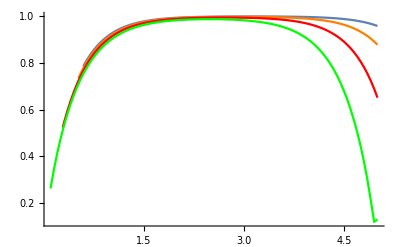

```mathematica
Block[
{qcrit,uz1,fu1,μextreme},
μextreme[uh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]/uh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
qcrit[us_,uh_,μ_,z_,θ_]:=us^(θ/2-z)Sqrt[1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z))]/(μ(1-(us/uh)^(z-θ)));
uz1[q_,us_,uh_,μ_,z_,θ_]:=NDSolveValue[
{-(q (z-θ) μ (u[t]/uh)^(z-θ))/u[t]-((-2+θ) u[t]^(-2+θ/2) u'[t]^2)/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(θ/2) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-(u[t]^(-1+θ/2) (((-2-z+θ) u[t]^(3-2 z) (u[t]/uh)^(z-θ))/uh^2-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(3-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(3-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)+(2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))+((-((2+z-θ) (u[t]/uh)^(1+z-θ))/uh-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(1+2 z-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(1+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)) u'[t]^2)/(-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2))/(2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-1/2 (-2+θ) u[t]^(-2+θ/2) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))-(u[t]^(-1+θ/2) u''[t])/((1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(-1+θ/2) u'[t] ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) u'[t]+1/(2 uh^2 (2-θ))u[t]^(3-2 z) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^3)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)-(2 u'[t] u''[t])/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) (u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))^(3/2))==0,u[0]== us,u'[0]==0},u,{t,0.1,5.7}
];
fu1[t_,q_,us_,uh_,μ_,z_,θ_]:=uz1[q,us,uh,μ,z,θ][t];
Show[
ListLinePlot[Table[{i,Abs[fu1[i,qcrit[0.1,1,0.75μextreme[1,1.5,0.1],1.5,0.1],0.1,1,0.75μextreme[1,1.5,0.1],1.5,0.1]]},{i,0.1,5,0.05}]],
ListLinePlot[Table[{i,Abs[fu1[i,qcrit[0.1,1,0.75μextreme[1,1.5,0.3],1.5,0.3],0.1,1,0.75μextreme[1,1.5,0.3],1.5,0.3]]},{i,0.1,5,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[fu1[i, qcrit[0.1,1,0.75μextreme[1,1.5,0.5],1.5,0.5],0.1,1,0.75μextreme[1,1.5,0.5],1.5,0.5]]},{i,0.1,5,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[fu1[i,qcrit[0.1,1,0.75μextreme[1,1.5,0.7],1.5,0.7],0.1,1,0.75μextreme[1,1.5,0.7],1.5,0.7]]},{i,0.1,5,0.05}],PlotStyle->Green],
PlotRange->{{0.1,5},All},AxesOrigin->{0,0}
]
]
```

```mathematica
Block[
{qcrit,uz1,fu1,μextreme},
μextreme[uh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]/uh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
qcrit[us_,uh_,μ_,z_,θ_]:=us^(θ/2-z)Sqrt[1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z))]/(μ(1-(us/uh)^(z-θ)));
uz1[q_,us_,uh_,μ_,z_,θ_]:=NDSolveValue[
{-(q (z-θ) μ (u[t]/uh)^(z-θ))/u[t]-((-2+θ) u[t]^(-2+θ/2) u'[t]^2)/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(θ/2) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-(u[t]^(-1+θ/2) (((-2-z+θ) u[t]^(3-2 z) (u[t]/uh)^(z-θ))/uh^2-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(3-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(3-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)+(2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))+((-((2+z-θ) (u[t]/uh)^(1+z-θ))/uh-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(1+2 z-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(1+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)) u'[t]^2)/(-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2))/(2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-1/2 (-2+θ) u[t]^(-2+θ/2) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))-(u[t]^(-1+θ/2) u''[t])/((1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(-1+θ/2) u'[t] ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) u'[t]+1/(2 uh^2 (2-θ))u[t]^(3-2 z) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^3)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)-(2 u'[t] u''[t])/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) (u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))^(3/2))==0,u[0]== us,u'[0]==0},u,{t,0.1,5.7}
];
fu1[t_,q_,us_,uh_,μ_,z_,θ_]:=uz1[q,us,uh,μ,z,θ][t];
Show[
ListLinePlot[Table[{i,Abs[fu1[i,0.5qcrit[0.1,1,0.75μextreme[1,1.5,0.1],1.5,0.1],0.1,1,0.75μextreme[1,1.5,0.1],1.5,0.1]]},{i,0.1,5,1}]],
ListLinePlot[Table[{i,Abs[fu1[i,0.5qcrit[0.1,1,0.75μextreme[1,1.5,0.3],1.5,0.3],0.1,1,0.75μextreme[1,1.5,0.3],1.5,0.3]]},{i,0.1,5,1}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[fu1[i,0.5qcrit[0.1,1,0.75μextreme[1,1.5,0.5],1.5,0.5],0.1,1,0.75μextreme[1,1.5,0.5],1.5,0.5]]},{i,0.1,5,1}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[fu1[i,0.5qcrit[0.1,1,0.75μextreme[1,1.5,0.7],1.5,0.7],0.1,1,0.75μextreme[1,1.5,0.7],1.5,0.7]]},{i,0.1,5,1}],PlotStyle->Green],
PlotRange->{{0.1,5},All},AxesOrigin->{0,0}
]
]
```

$Aborted

```mathematica
Block[
{qcrit,uz1,fu1,μextreme},
μextreme[uh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]/uh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
qcrit[us_,uh_,μ_,z_,θ_]:=us^(θ/2-z)Sqrt[1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z))]/(μ(1-(us/uh)^(z-θ)));
uz1[q_,us_,uh_,μ_,z_,θ_]:=NDSolveValue[
{-(q (z-θ) μ (u[t]/uh)^(z-θ))/u[t]-((-2+θ) u[t]^(-2+θ/2) u'[t]^2)/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(θ/2) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-(u[t]^(-1+θ/2) (((-2-z+θ) u[t]^(3-2 z) (u[t]/uh)^(z-θ))/uh^2-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(3-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(3-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)+(2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))+((-((2+z-θ) (u[t]/uh)^(1+z-θ))/uh-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(1+2 z-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(1+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)) u'[t]^2)/(-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2))/(2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-1/2 (-2+θ) u[t]^(-2+θ/2) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))-(u[t]^(-1+θ/2) u''[t])/((1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(-1+θ/2) u'[t] ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) u'[t]+1/(2 uh^2 (2-θ))u[t]^(3-2 z) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^3)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)-(2 u'[t] u''[t])/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) (u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))^(3/2))==0,u[0]== us,u'[0]==0},u,{t,0.1,5.7}
];
fu1[t_,q_,us_,uh_,μ_,z_,θ_]:=uz1[q,us,uh,μ,z,θ][t];
Show[
ListLinePlot[Table[{i,Abs[fu1[i,qcrit[0.1,1,0.75μextreme[1,2,1],2,1],0.1,1,0.75μextreme[1,2,1],2,1]]},{i,0.1,5,1}]],
ListLinePlot[Table[{i,Abs[fu1[i,qcrit[0.1,1,0.75μextreme[1,4,1],4,1],0.1,1,0.75μextreme[1,4,1],4,1]]},{i,0.1,5,1}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[fu1[i,qcrit[0.1,1,0.75μextreme[1,6,1],6,1],0.1,1,0.75μextreme[1,6,1],6,1]]},{i,0.1,5,1}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[fu1[i,qcrit[0.1,1,0.75μextreme[1,8,1],8,1],0.1,1,0.75μextreme[1,8,1],8,1]]},{i,0.1,5,1}],PlotStyle->Green],
PlotRange->{{0.1,5},All},AxesOrigin->{0,0}
]
]
```

$Aborted